```mathematica
(* Teardrop shape for use with magma chambers and blobs. *)
```

```mathematica
teardropFormula:={Cos[t]+Max[0,Cos[t]],Sin[t]*(1-Max[0,Cos[t]]^2)}
```

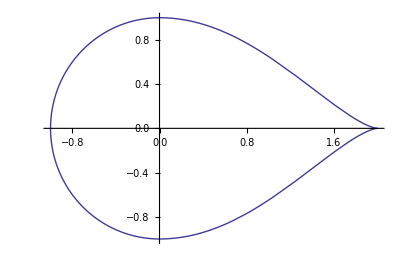

```mathematica
ParametricPlot[teardropFormula,{t,0,2*π}]
```

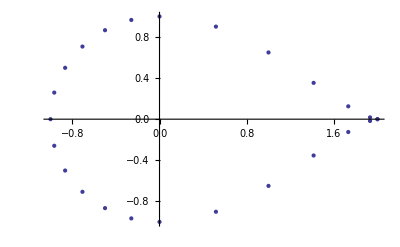

```mathematica
ListPlot[Table[teardropFormula,{t,0,2*π,π/12}]]
```

```mathematica
topFromTangent[v_]:={v[[2]],-v[[1]]}
```

```mathematica
bottomFromTangent[v_]:={-v[[2]],v[[1]]}
```

```mathematica
(* curvature for the subduction angle made up piecewise of lines and arcs *)
```

```mathematica
(* the ideal line is parametereized by t, with t0=0 being placed where the flat portion starts bending down *)
```

```mathematica
t0:=0
```

```mathematica
t1:=θ0*r0
```

```mathematica
t2:=t1+θ1*r1
```

```mathematica
t3:=t2+θ2*r2
```

```mathematica
(* c vectors are centers of the arcs that are there *)
```

```mathematica
c0:={d,y0-r0}
```

```mathematica
p0[t_]:= {d-t,y0}
```

```mathematica
pd0[t_]:={-1,0}
```

```mathematica
p1[t_]:=Module[{θ=π/2+(t-t0)/r0},c0+r0*{Cos[θ],Sin[θ]}]
```

```mathematica
pd1[t_]:=bottomFromTangent[Normalize[p1[t]-c0]]
```

```mathematica
c1:=p1[t1]+r1*Normalize[c0-p1[t1]]
```

```mathematica
p2[t_]:=Module[{θ=π/2+θ0+(t-t1)/r1},c1+r1*{Cos[θ],Sin[θ]}]
```

```mathematica
pd2[t_]:=bottomFromTangent[Normalize[p2[t]-c1]]
```

```mathematica
c2:=p2[t2]+r2*Normalize[c1-p2[t2]]
```

```mathematica
p3[t_]:=Module[{θ=π/2+θ0+θ1+(t-t2)/r2},c2+r2*{Cos[θ],Sin[θ]}]
```

```mathematica
pd3[t_]:=bottomFromTangent[Normalize[p3[t]-c2]]
```

```mathematica
dir4:=Module[{θ=θ0+θ1+θ2+π},{Cos[θ],Sin[θ]}]
```

```mathematica
p4[t_]:=p3[t3]+(t-t3)*dir4
```

```mathematica
pd4[t_]:=dir4
```

```mathematica
makeTop[f_,fd_,t_]:=f[t]+topFromTangent[fd[t]]*m
```

```mathematica
makeBottom[f_,fd_,t_]:=f[t]-topFromTangent[fd[t]]*m
```

```mathematica
(* with actual values *)
```

```mathematica
rules:={
d->2,
y0->(-3000-10000)/2, (* between top and bottom oceanic crust *)
m->0.5,
θ0->π/12,
r0->4,
θ1->π/12,
r1->2,
θ2->π/12,
r2->4}
```

```mathematica
ptop0[-1]/.rules
```

{3,-13500}

```mathematica
tright:=-5
```

```mathematica
tleft:=t3+5
```

```mathematica
xPadding:=5
```

```mathematica
xRange:={p4[tleft][[1]]-xPadding,p0[tright][[1]]+xPadding}/.rules
```

```mathematica
yPadding:=5
```

```mathematica
yRange:={p4[tleft][[2]]-yPadding,p0[tright][[2]]+yPadding}/.rules
```

```mathematica
segment[position_,derivative_,tStart_,tEnd_,color_]:={
(* middle line *)
ParametricPlot[position[t]/.rules,{t,tStart,tEnd},PlotStyle->color],

(* top *)
ParametricPlot[makeTop[position,derivative,t]/.rules,{t,tStart,tEnd},PlotStyle->{color,Dashed}],

(* bottom *)
ParametricPlot[makeBottom[position,derivative,t]/.rules,{t,tStart,tEnd},PlotStyle->{color,Dashed}]
}
```

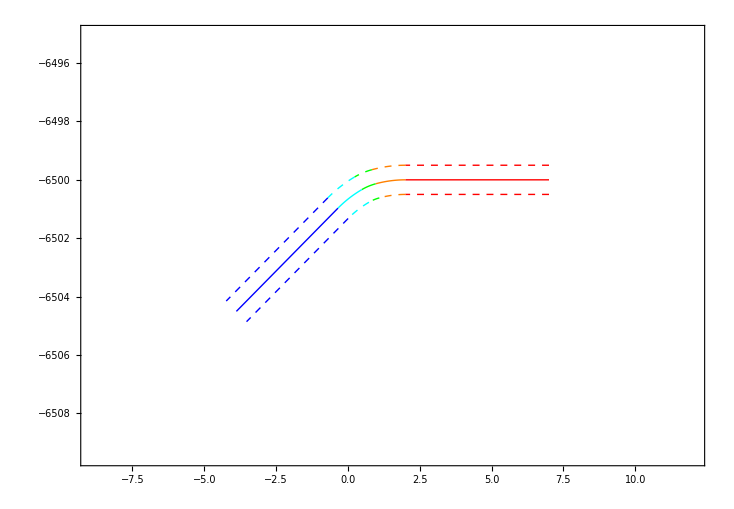

```mathematica
Show[
Flatten[{segment[p0,pd0,tright,t0,Red],
segment[p1,pd1,t0,t1/.rules,Orange],
segment[p2,pd2,t1/.rules,t2/.rules,Green],
segment[p3,pd3,t2/.rules,t3/.rules,Cyan],
segment[p4,pd4,t3/.rules,tleft/.rules,Blue]}],
PlotRange->{xRange,yRange},Frame->True]
```